# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\quantum_chaotic_channels\MG files\LMG chain

```mathematica
Get["C:\\Users\\Miguel\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# LMG

## Definitions

```mathematica
(*Operadores*)
Clear[Sz,SM,Sm,Sx,Sy,Qp,Q,P];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
Qp[J_]:=DiagonalMatrix[Table[Sqrt[i/2],{i,IntegerPart[2J]}],-1];
Q[J_]:=Qp[J]+Transpose[Qp[J]];
P[J_]:=-I(Qp[J]-Transpose[Qp[J]]);
Clear[H];
H[J_,α_,k_]:=N[(k/(2J))(Sx[J].Sx[J])+(α)(Sz[J])];

(*Coherent states*)
Clear[z];
z[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];

(*Stuff to partition the system*)
Clear[CG];
CG[n1_,n_,N1_,N2_]:=CG[n1,n,N1,N2]=Binomial[N1,n1]*Binomial[N2,n-n1]/Binomial[N1+N2,n];
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.1],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
```

## Hamiltonian

## Hamiltonian

```mathematica
J=100;
α=0.84;
k=-2;
```

```mathematica
Clear[mat,neweigenvec];
mat=H[J,α,k];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Transpose[Sort[Transpose[Eigensystem[matM]]]];
{eigenvalm,eigenvecm}=Transpose[Sort[Transpose[Eigensystem[matm]]]];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
iprs=ParallelTable[Total[Quiet[Abs[i]^4]],{i,neweigenvec}];
```

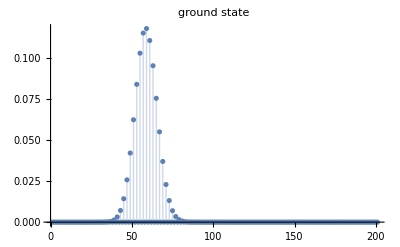

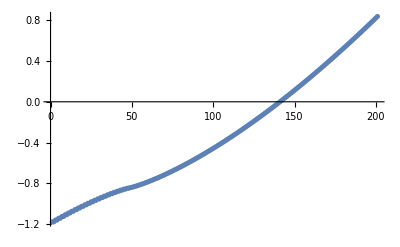

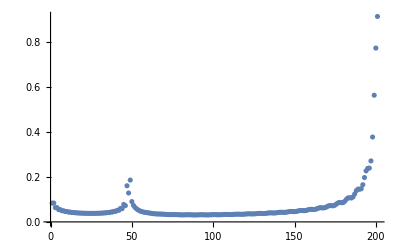

```mathematica
ListPlot[Quiet[Abs[neweigenvec[[1]]]^2],PlotRange->All,Filling->Axis,PlotLabel->Style["ground state",25,Black]]
ListPlot[neweigenval/J,PlotRange->All]
ListPlot[iprs,PlotRange->All]
```

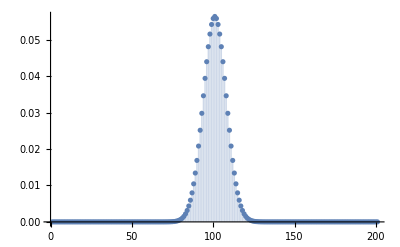

```mathematica
{Q,P}={1,1};
ini=z[J,Q,P];
iniprofile=ListPlot[Quiet[Abs[ini]^2],PlotRange->All,Filling->Axis]
```

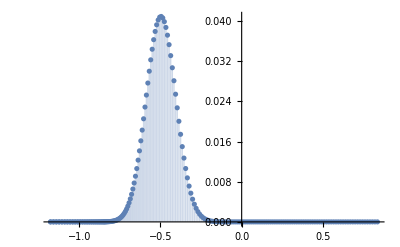

```mathematica
inilmg=Conjugate[neweigenvec].ini;
ipr=Total[Quiet[Abs[inilmg]^4]];
ListPlot[Transpose[{neweigenval/J,Quiet[Abs[inilmg]^2]}],PlotRange->All,Filling->Axis]
```

```mathematica
Clear[sur];
sur[ini_,n_]:=Module[{a},
Abs[(Exp[-I*n*neweigenval]).Abs[ini]^2]^2
];
```

```mathematica
numberOftemporalPoints=500;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,4},{x,#/5,1,-1}]]&[numberOftemporalPoints];
```

```mathematica
data=ParallelTable[sur[inilmg,t],{t,tlist}];
```

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
```

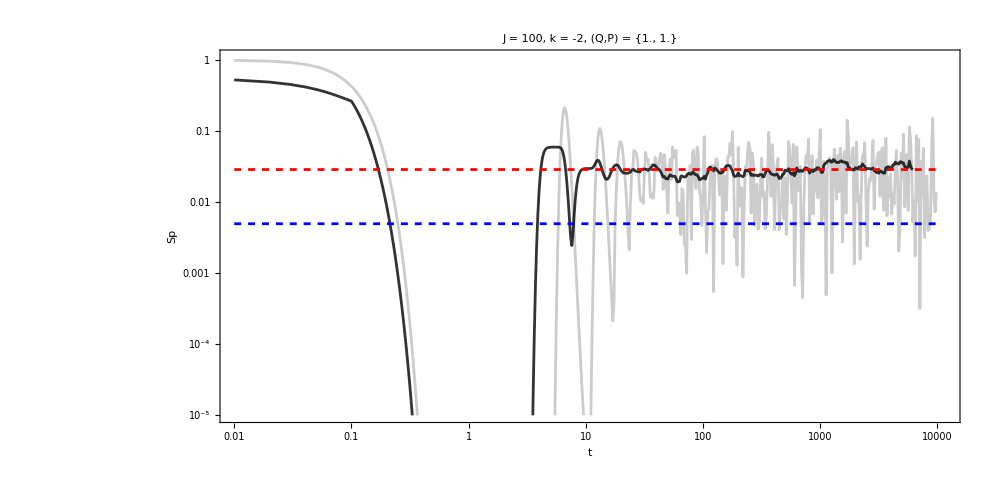

```mathematica
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1/2,ImageSize->1000],plot2}]
```

## Reduced density matrix

```mathematica
{Q,P}={1,1};
ini=z[J,Q,P];
```

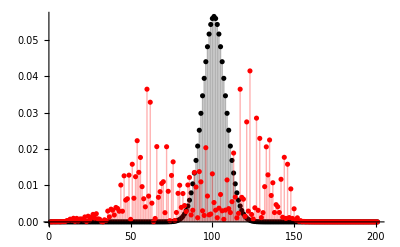

```mathematica
tf=10000;
ψt=StateEvolution[tf,ini,neweigenval,neweigenvec];
iniprofile=ListPlot[Quiet[Abs[ini]^2],PlotRange->All,Filling->Axis,PlotStyle->Black];
laterprofile=ListPlot[Quiet[Abs[ψt]^2],PlotRange->All,Filling->Axis,PlotStyle->Red];
Show[{iniprofile,laterprofile},ImageSize->400,PlotRange->All]
```

```mathematica
newtlist=Range[0,1000];
ψts=ParallelTable[StateEvolution[t,ini,neweigenval,neweigenvec],{t,newtlist}];
```

```mathematica
Clear[J,N1,N2];
J=100;
N1=1; (*Here, I'm partitioning the system of N=2J=200 spins in subsystem N1 with 1 spin and N2 with 199 spins*)
N2=2J-N1;
rhos={};
rho=ConstantArray[0,{N1+1,N1+1}];
```

```mathematica
rhos={};
Do[
b=ψts[[i]];
Do[
rho[[i,j]]=Sum[ b[[i+n2-1]]*Conjugate[b[[j+n2-1]]]*Sqrt[CG[i-1,i+n2-2,N1,N2]*CG[j-1,j+n2-2,N1,N2]],{n2,1,N2+1}];
rho[[j,i]]=Conjugate[rho[[i,j]]];
,{i,1,N1+1},{j,i,N1+1}];
AppendTo[rhos,Chop[rho]];
,{i,Length[ψts]}];
```

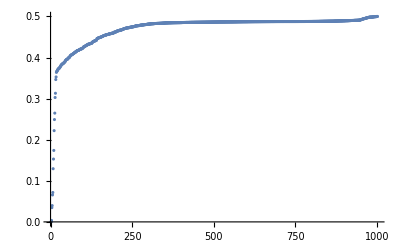

```mathematica
linearentropya=ListPlot[Sort[Table[1-Chop[Tr[i.i]],{i,rhos}]],PlotRange->All]
```

### Bloch Plots

```mathematica
blochs=Table[bloch[i],{i,rhos}];
plotpuntosini=ListPointPlot3D[{blochs[[1]]},PlotStyle->Black,PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
plotpuntos=ListPointPlot3D[blochs[[2;;-1]],ColorFunction->"Rainbow",PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
Show[{plotpuntos,plotpuntosini},plotsphere,ImageSize->400,PlotLabel->Style["k = "<>ToString[N[k]]<>", N = "<>ToString[J]<>", n1 = "<>ToString[N1],25,Black]]
```

-Graphics3D-

# Quantum map

## LDoS

## Hamiltonian

```mathematica
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
L=10(*number of spins*);
{hx,hz,J}={1,0.8,ConstantArray[1,L-1]};
```

{0.501259,0.520359}

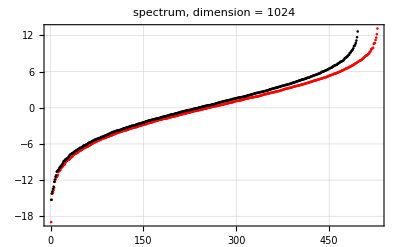

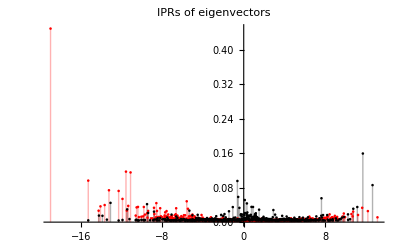

-Graphics-

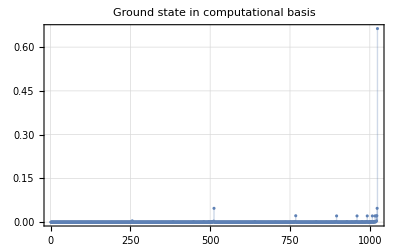

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
OddEigVals=Complement[eigVals,EvenEigVals];
OddEigVecs=Complement[eigVecs,evenEigenVecs];
{MeanLevelSpacingRatio[OddEigVals],MeanLevelSpacingRatio[EvenEigVals]}
ListPlot[{EvenEigVals,OddEigVals},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Red,Black},ImageSize->400,PlotLabel->Style["spectrum, dimension = "<>ToString[2^L],25,Black]]
iprM=ParallelTable[Total[Quiet[Abs[i]^4]],{i,evenEigenVecs}];
iprm=ParallelTable[Total[Quiet[Abs[i]^4]],{i,OddEigVecs}];
ListPlot[{Transpose[{EvenEigVals,iprM}],Transpose[{OddEigVals,iprm}]},PlotRange->All,Filling->Axis,ImageSize->400,PlotStyle->{Red,Black},PlotLabel->Style["IPRs of eigenvectors",25,Black]]
MatrixPlot[H,PlotRange->All,PlotTheme->"Detailed"]
ListPlot[Abs[eigVecs[[1]]]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->400,PlotLabel->Style["Ground state in computational basis",25,Black]]
```

## Initial state all random

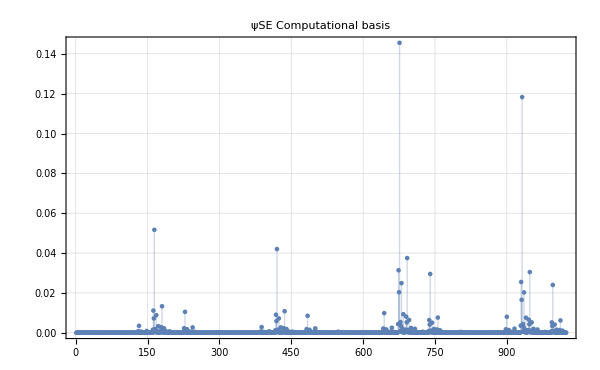
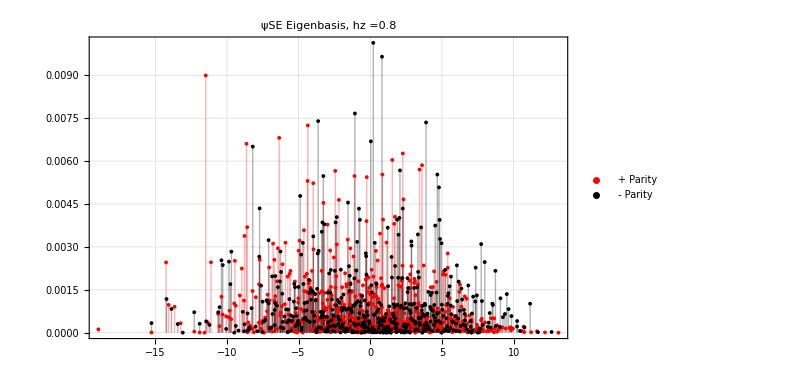

```mathematica
ψ0E=RandomChainProductState[L];
ψ0Espineven=Conjugate[evenEigenVecs].ψ0E;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0E;
plota=ListPlot[Abs[ψ0E]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state coherent state

```mathematica
Clear[ψ0SE];
a=RandomReal[];
state=qubit[a,a];
ψ0SE=coherentstate[state,L];
a
```

0.901702

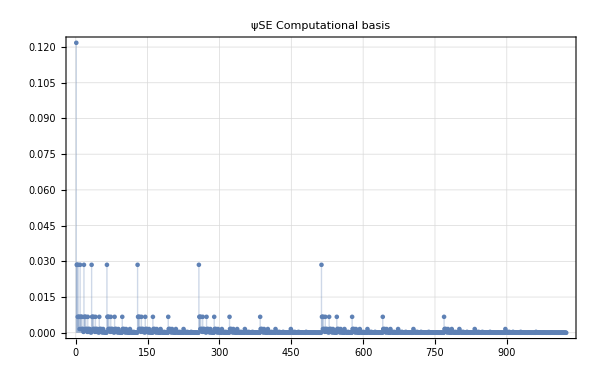
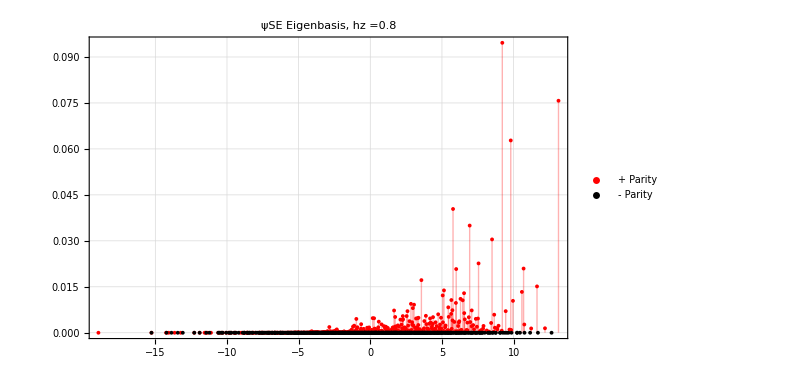

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

```mathematica
Clear[ψ0SE];
state=qubit[Pi/4,Pi/4];
ψ0SE=coherentstate[state,L];
```

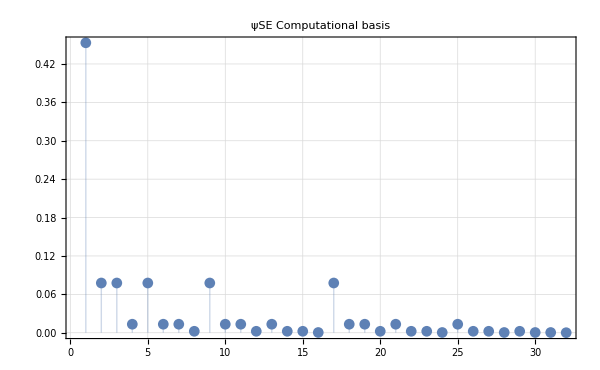
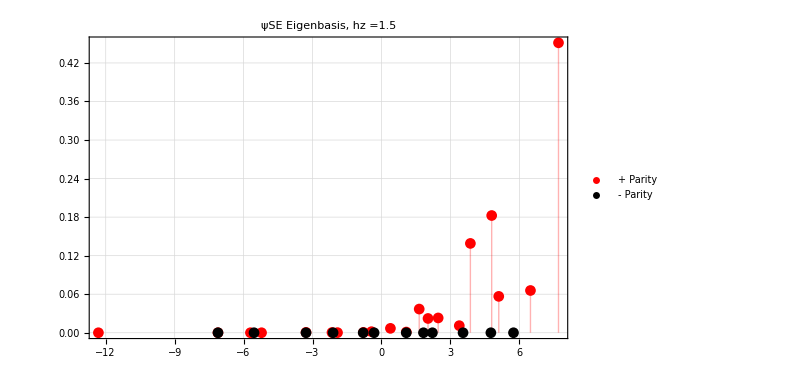

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## 0<=t<=5

```mathematica
?Superoperator
```

```mathematica
ψT={coherentstate[qubit[RandomReal[],RandomReal[]],L-1],VectorFromKetInComputationalBasis[ConstantArray[1,L-1]],RandomChainProductState[L-1]};
```

```mathematica
styles={Style["Coherent state, h_z = "<>ToString[hz],50,Black],Style["Up state, h_z = "<>ToString[hz],50,Black],Style["Random product state, h_z = "<>ToString[hz],50,Black]};
```

```mathematica
tf=2.0;
```

```mathematica
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
];,{t,0,tf,.1}];
AppendTo[listplots,
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","eigenvalues( Choi )"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]];
,{i,3}]
```

```mathematica
t=1.4;
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
```

```mathematica
Export["test_L_10_h_0.8.png",testimage,ImageSize->4000,ImageResolution->400]
```

test_L_10_h_0.8.png

```mathematica
grids=Table[Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All],{t,0,tf,0.1}];
```

```mathematica
Table[Export["h_z_"<>ToString[hz]<>"_frame_"<>ToString[i]<>".png",grids[[i]],ImageSize->1000,ImageResolution->300],{i,3}]
```

{h_z_1.5_frame_1.png,h_z_1.5_frame_2.png,h_z_1.5_frame_3.png}